# Лабораторная работа № 6. Доска Гальтона.

Вычислительная практика 2019-2020.
1 курс. 5 группа.
Кушнеров А.В.

## Общие теоретические сведения

Доска Гальтона - устройство изобретённое Фрэнсисом Гальтоном. Доска представляет собой специальное поле с засечками в определённой последовательности, сквозь которые, через верхнюю точку бросается некоторое количество шариков. 
-Graphics-
Наша задача в лабораторной работе смоделировать в виде анимации работу данного устройства.

## Моделирование доски

Как вы можете заметить, структура доски Гальтона в точности совпадает с геометрической интерпретацией треугольного числа. Для изображения доски Гальтона воспользуйтесь наработками из ЛР5.

### Задание 1.

Реализуйте функцию для нахождения координат точек доски Гальтона, используя наработки из ЛР5.

```mathematica
tr[n_]:=NestList[(#+{-1/2,(-√3)/2})&,{1/2*#,-(√3)/2#},n-1-#]&/@Range[0,n-1]
```

```mathematica
newcr[n_]:=(tr[n][[#]]⟦-1⟧)&/@Range[n]
```

```mathematica
newl[n_]:=newcr[#]&/@Range[n]
```

```mathematica
new=newl[12];
```

## Моделирование движения точки

Движение точки осуществляется по точкам доски. Установим ряд правил для него.

1. Шарик может находиться только в одной из точек доски.
2. Каждый следующий шаг шарик опускается на один ряд вниз.
3. Из заданной точки шарик может оказаться только в соседней (в нижнем ряду).
4. Шарик не выходит за пределы треугольника.
5. Шарики поступают последовательно. Пока одна точка на доске, новая не поступает.

Теперь можно приступать к непосредственному моделированию движения точки. Вспомним, что из ЛР5 у нас сохранились списки координат точек, из каждой строки треугольного числа (или Доски Гальтона).

Для того, чтобы организовать движение по доске занумеруем (условно и только в голове), точки в каждой строке.  Наша доска в таком случае будет иметь понятную структуру.

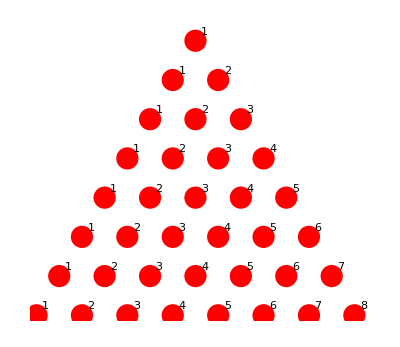

-Graphics-

Движение шарика непосредственно будет отрисовано подсвечиванием чёрным цветом текущего положения (по желанию можете соединить точки маршрута отрезками). На примере ниже показано движение свежепоступивщего шарика от начала до конца доски.

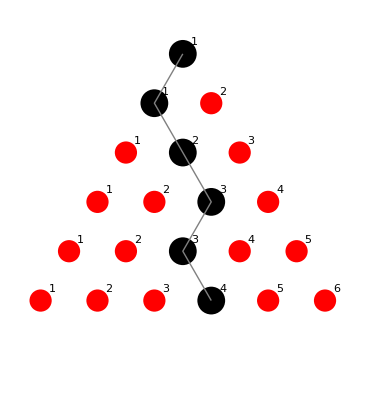

-Graphics-

Без труда можно записать маршрут шарика по треугольнику - (1,1,2,3,3,4). Именно такими маршрутами и определяется прохождения шарика в нашей модели. Очевидно, что у всех маршрутов, исходя из  наших правил, есть одна особенность. Каждый следующий шаг маршрута либо равен предыдущему, либо отличается от него на 1 в большую сторону. 
Используя комбинаторику и функции Append и Nest, можно быстро отыскать все возможные маршруты прохождения шарика для заданной доски.

### Задание 2.

Реализуйте функцию для нахождения всех возможных маршрутов на доске Гальтона заданного размера.

```mathematica
Rout[m_List]:={Append[#,Last[#]],Append[#,Last[#]+1]}&/@m//Flatten[#,1]&
```

```mathematica
difRout[n_]:=Nest[Rout,{{1}},n-1]
```

```mathematica
routs=difRout[12];
```

## Реализация анимации движения.

Теперь приступим к созданию мультика. Предположим, что на нашу доску высыпают 100 шариков. Для каждого шарика случайным образом выберем маршрут из списка всех маршрутов.

```mathematica
rote={RandomChoice[routs]}
```

{{1,2,2,2,2,2,2,2,2,2,2,2}}

```mathematica
points=ReplacePart[rote,{i_,j_}:>new⟦j,rote⟦i,j⟧⟧]
```

{{{0,0},{1/2,-(√3)/2},{0,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3},{-3/2,-(5 √3)/2},{-2,-3 √3},{-5/2,-(7 √3)/2},{-3,-4 √3},{-7/2,-(9 √3)/2},{-4,-5 √3},{-9/2,-(11 √3)/2}}}

```mathematica
pointlist=Table[RandomChoice[routs],{100}];
```

```mathematica
coordinateList=First[ReplacePart[{#},{i_,j_}:>new⟦j,{#}⟦i,j⟧⟧]]&/@pointlist;
```

После этого, мы уже можем отрисовать движение шарика с помощью операторов Line, Point. Ведь мы знаем, что на “первом этаже” шарик попал в первую точку, на “втором этаже” на вторую и т.д. Используя функцию Part или ReplaсePart мы извлекаем необходимые координаты из списка координат точек доски.

-Graphics-

### Задание 3.

Использую функции Graphiсs и ListAnimate. Реализуйте анимацию последовательного поступления некоторого количества шариков на доску заданного размера.

## Отслеживание статистики количества точек.

Как говорилось ранее, точки поступают последовательно. Наш алгоритм предполагает выбор случайного маршрута для каждой точки. Очевидно, что точки могут закончить своё движение в разных позициях последнего ряда. Подсчёт точного количества точек завершивших маршрут на определённом месте представляет определённый интерес. 
В нашем случае, конечное положение точки, определено в последней координате маршрута.

### Задание 4.

Добавьте в функцию из задания 3 возможность отслеживания количества точек, которые завершили маршрут в определённом месте.

Пример.

```mathematica
textlist=Last[new]⟦#⟧+{0,-(√3)/2}&/@Range[Length[new]];
```

```mathematica
lastpoints=Last[coordinateList⟦#⟧]&/@Range[Length[coordinateList]];
```

```mathematica
lastel=new//Last;
```

```mathematica
text={0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
mil[i_]:=If[lastpoints⟦i⟧==lastel⟦#⟧,ReplacePart[text,#-> text[[#]]+1]]&/@Range[12]//DeleteCases[#,Null]&//Flatten
```

```mathematica
m[n_]:=Plus@@(mil[#]&/@Range[n])
```

```mathematica
mil1[i_,l1_,l2_,trn_]:=If[l1⟦i⟧==l2⟦#⟧,ReplacePart[text,#-> text[[#]]+1]]&/@Range[trn]//DeleteCases[#,Null]&//Flatten
```

```mathematica
m1[n_,l1_,l2_,trn_]:=Plus@@(mil1[#,l1,l2,trn]&/@Range[n])
```

```mathematica
m1[12,lastpoints,lastel,12]
```

{0,0,0,0,3,2,3,2,2,0,0,0}

```mathematica
graphpos=Last[new]⟦#⟧+{-.5,-3}&/@Range[Length[new]]//Append[#,Last[#]+{1,0}]&;
```

```mathematica
animationList=Table[Graphics[{{PointSize[0.04],Red,Point[#]&/@#}&/@new,{Blue,Text[Style[i,Large],{-5,0}],Black,PointSize[0.05],Point[coordinateList⟦i⟧],Dashed,Thin,Line[coordinateList⟦i⟧]},{EdgeForm[Directive[Dashed,Pink]],Transparent,Rectangle[graphpos⟦#⟧,graphpos⟦#+1⟧+{0,√3}]&/@Range[12]},{Text[Style[m[i]⟦#⟧,Large],textlist⟦#⟧]}&/@Range[12],EdgeForm[Directive[Thick,Red]],{Rectangle[graphpos⟦#⟧,graphpos⟦#+1⟧+{0,(√3*m[i]⟦#⟧)/100}]}&/@Range[12],Text[Style[#,Red,Large],textlist⟦#⟧+{0,-(3 √3)/2}]&/@Range[Length[textlist]]}],{i,1,Length@coordinateList}];
```

```mathematica
func[trn_,n_]:=Block[{new,routs,pointlist,coordinateList,textlist,lastpoints,lastel,graphpos,l},
new=newl[trn];
routs=difRout[trn];
pointlist=Table[RandomChoice[routs],{n}];
textlist=Last[new]⟦#⟧+{0,-(√3)/2}&/@Range[Length[new]];
coordinateList=First[ReplacePart[{#},{i_,j_}:>new⟦j,{#}⟦i,j⟧⟧]]&/@pointlist;
lastpoints=Last[coordinateList⟦#⟧]&/@Range[Length[coordinateList]];
lastel=new//Last;
graphpos=Last[new]⟦#⟧+{-.5,-3}&/@Range[Length[new]]//Append[#,Last[#]+{1,0}]&;
l=Table[Graphics[{{PointSize[0.04],Red,Point[#]&/@#}&/@new,{Blue,Text[Style[i,Large],{-5,0}],Black,PointSize[0.05],Point[coordinateList⟦i⟧],Dashed,Thin,Line[coordinateList⟦i⟧]},{EdgeForm[Directive[Dashed,Pink]],Transparent,Rectangle[graphpos⟦#⟧,graphpos⟦#+1⟧+{0,√3}]&/@Range[trn]},{Text[Style[m1[i,lastpoints,lastel,trn]⟦#⟧,Large],textlist⟦#⟧]}&/@Range[trn],EdgeForm[Directive[Thick,Red]],{Rectangle[graphpos⟦#⟧,graphpos⟦#+1⟧+{0,(√3*m1[i,lastpoints,lastel,trn]⟦#⟧)/n}]}&/@Range[trn],Text[Style[#,Red,Large],textlist⟦#⟧+{0,-(3 √3)/2}]&/@Range[Length[textlist]]}],{i,1,Length@coordinateList}];
ListAnimate[l,DefaultDuration->100]]
func[10,3000]
```

```mathematica
ListAnimate[animationList,DefaultDuration->100]
```

## Добавление корзин*

В реальной доске Гальтона шарики падают в корзинки после прохождения маршрута. В зависимости от последней точки в маршруте - шарик падает в определённую корзину.

-Graphics-

### Задание 5*

Добавьте в вашу анимацию заполнение корзин в конце доски.

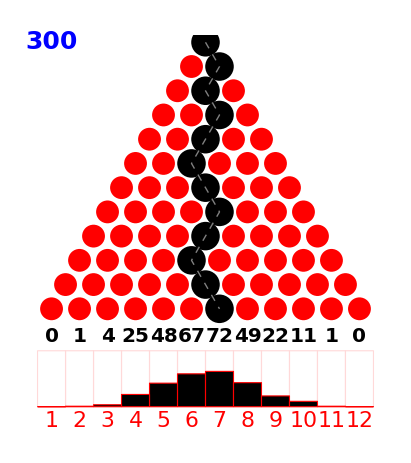

-Graphics-